```mathematica
getFullGrid[n_,m_]:=Table[{1,1},{i,n},{j,m}]

getGridSymplex[{x_,y_}]:=With[{a=Floor[x],b=Floor[y]},{{a,b},Boole[Not[(1-(x-a)>=y-b)]] +1}]
isInGrid[grid_,n_,m_,{x_,y_}]:=
Module[
{p ,i ,j,q
},
If[0<=x≤n&&0≤y≤m,
If[(
p=getGridSymplex[{x,y}];
i=p[[1,1]];
j=p[[1,2]];
q=p[[2]];
grid[[i+1,j+1,q]]==1),1,0],
0]
]
getSymplexVertexForm[{{a_,b_},1}]:={{a,b},{a+1,b},{a,b+1}}
getSymplexVertexForm[{{a_,b_},2}]:={{a+1,b+1},{a+1,b},{a,b+1}}

getBarycetricCordinates[p_,{v_,1}]:=Module[{x=p-v,a,b},(a=x[[1]];b=x[[2]];{1-a-b,a,b})]
getBarycetricCordinates[p_,{v_,2}]:=Module[{x=p-v-{1,1},a,b},
(a=x[[1]];b=x[[2]];{1+a+b,-a,-b})]

turnSymplexToGridForm[{v1_,v2_,v3_}]:=getGridSymplex[(v1+v2+v3)*(1/3)]

getAllSymplexes[grid_,n_,m_]:=Module[{f,ver,edges},

(ver[{{x1_,x2_},{y1_,y2_},{z1_,z2_}}]:={{{x1,x2}},{{y1,y2}},{{z1,z2}}};
edges[{{x1_,x2_},{y1_,y2_},{z1_,z2_}}]:={{{x1,x2},{y1,y2}},{{y1,y2},{z1,z2}},{{x1,x2},{z1,z2}}};
f[{i_,j_},{0,0}]:={};
f[{i_,j_},{1,0}]:=Union[{{{i-1,j-1},{i,j-1},{i-1,j}}},ver[{{i-1,j-1},{i,j-1},{i-1,j}}],edges[{{i-1,j-1},{i,j-1},{i-1,j}}]];
f[{i_,j_},{0,1}]:=Union[{{{i,j},{i,j-1},{i-1,j}}},ver[{{i,j},{i,j-1},{i-1,j}}],edges[{{i,j},{i,j-1},{i-1,j}}]];
f[{i_,j_},{1,1}]:=Union[f[{i,j},{0,1}],f[{i,j},{1,0}]];
DeleteDuplicates[Flatten[Map[f[#,grid[[#[[1]],#[[2]]]]]&,Flatten[Table[{i,j},{i,n},{j,m}],1]],1]]

)]

getAll2Dsymplexes[grid_,n_,m_]:=Select[getAllSymplexes[grid,n,m],Length[#]==3&]

getFullDiscreateVectorField[grid_,n_,m_]:=Map[{#,#}&,getAllSymplexes[grid,n,m]]
getFullDiscreateVectorField[vectors_,grid_,n_,m_]:=
Module[{
s =getAllSymplexes[grid,n,m],
w =DeleteDuplicates[Flatten[vectors,1]],
rest 
},

(rest=Complement[s,w,SameTest->(SubsetQ[#1,#2]&& SubsetQ[#2,#1]&)];
Union[vectors,Map[{#,#}&,rest]]
)

]

getCommonVectors[vectorField_,symplex_]:=Module[
{f},
(
f[{head_,tail_}]:=SubsetQ[symplex,head];
Select[vectorField,f])

]

 
fieldForDiscreateVector[x_,w_,eps_,d_]:=Module[{h,g,theta,dzeta,eta,tailCom,headCom,f,f1,tail,head}
,

(

tail=w[[1]];
head=w[[2]];
tailCom=Complement[{1,2,3},tail];
headCom=Complement[{1,2,3},head];
g[s_]:=CubeRoot[eps^2*s];
eta[s_,p_]:=If[0<=s≤eps/(8*d)&& Total[p[[headCom]]^2]==0,1,((8*d)/eps)*Abs[s]];
h[s_]:= 1 /; (s≤eps/2)|| (eps*(3/2)<=s);
h[s_]:=1 +(eps +2)/2 - ((eps+2)/eps )* s /;  eps*(1/2)<=s≤eps;
h[s_]:=-2 - (3/2)*eps + ((eps+2)/eps )*s;
dzeta[s_,p_]:= eta [s,p]/; s<=eps/(8*d) ;
dzeta[s_,p_] :=h[s];
theta[p_]:=Min[Union[{eps},p[[tail]] -eps]];
f[verNum_ ,p_]:=-1*g[(p[[verNum]])]/; MemberQ[headCom,verNum]; 
f[verNum_ ,p_]:=dzeta[p[[verNum]],p ]+ theta[p] - Total[p[[headCom]]];

f1[verNum_,p_]:=If[MemberQ[tail,verNum],p [[verNum]] + (1/Length[tail])*(Total[p[[tailCom]] ] - Total[Map[f[#,p]&,tailCom ]]-1),f[verNum,p]];
{f1[1,x],f1[2,x],f1[3,x]}

)

]

isInVector[x_,{tail_,head_},eps_]:=AllTrue[x[[tail]],(#>=eps)&] &&AllTrue[x[[Complement[{1,2,3},head]]],(#≤eps)&]
GetVectorFieldForSymplex[x_,{w_},eps_,d_]:=fieldForDiscreateVector[x,w,eps,d]
GetVectorFieldForSymplex[x_,l_,eps_,d_]:=With[{w=First[l],r=Rest[l]},If[isInVector[x,w,eps],fieldForDiscreateVector[x,w,eps,d],GetVectorFieldForSymplex[x,r,eps,d]]]

getVectorsDictionary[vectorField_,grid_,n_,m_]:=
Module[{f,g},
(
g[x_]:=Module[{},1];
f[{vectors_,{orgin_,1}}]:=Module[{h},
(h[{0,0}]=1;
h[{1,0}]=2;
h[{0,1}]=3;
h[{1,1}]=4;
Map[h[#-orgin]&,vectors,{3}]
)];
f[{vectors_,{orgin_,2}}]:=Module[{h},
(h[{1,1}]=1;
h[{0,1}]=2;
h[{1,0}]=3;
h[{0,0}]=4;
Map[h[#-orgin]&,vectors,{3}]
)];

Association[Map[turnSymplexToGridForm[#]->f[{getCommonVectors[vectorField,#] ,turnSymplexToGridForm[#]}]&,getAll2Dsymplexes[grid,n,m]]]
)
 ]

GetVectorField[grid_,vectorField_,eps_,d_]:=
Module[
{n=Length[grid],m=Length[grid[[1]]],vectorsList ,vectorsDictionary},
(vectorsList =getFullDiscreateVectorField[vectorField,grid,n,m];
vectorsDictionary=getVectorsDictionary[vectorsList,grid,n,m];
Function[{x},
Module[{gridSymplex,type,vectors},
(
gridSymplex = getGridSymplex[x];
type = gridSymplex[[2]];
vectors = Lookup[vectorsDictionary,Key[gridSymplex],{}];
If[vectors ≠{}
,If[type==1
,GetVectorFieldForSymplex[getBarycetricCordinates[x,gridSymplex],vectors,eps,d][[{2,3}]]
,(-1)*GetVectorFieldForSymplex[getBarycetricCordinates[x,gridSymplex],vectors,eps,d][[{2,3}]]
]
,{0.,0.}
]

)
]
]
)
]


getPoints[S_]:=DeleteDuplicates[Flatten[S,1]]
getEdges[S_]:=Module [{f},
(f[{a_,b_,c_}]:={{a,b} ,{a,c},{c,b}};
DeleteDuplicates[Flatten[Map[f[#]&,S],1]]
)

]

getBarycentricCentre[s_]:=Total[s]/Length[s]
show2DSymplicialComplex[S_]:=Module[{points,edges},
points=Map[Point[#]&,getPoints[S]];
edges=Map[(Line[#])&,getEdges[S]];
Show[{
Graphics[{PointSize[0.03],Pink,points},Axes->True],
Graphics[{Thick,edges},Axes->True]
}
]
]
show2DVectorField[V_]:=Module[{showVector},
(
showVector[{tail_,head_}]:=
If[tail!=head,
Graphics[
{Green,Thick,Arrowheads[0.04],Arrow[{getBarycentricCentre[tail],getBarycentricCentre[head]}]},Axes->True],
Graphics[{Green,Circle[getBarycentricCentre[tail],0.04]},Axes->True]
];
Show[Map[showVector[#]&,V]]
)
]

drawFullPlot[grid_,vectorField_,eps_]:=Module[
{n=Length[grid],
m=Length[grid[[1]]],
fullVectorField,
P1,
P2,
P3,
f
},

(fullVectorField =getFullDiscreateVectorField[vectorField,grid,n,m];
P1 = show2DSymplicialComplex[getAll2Dsymplexes[grid,n,m]];
P2 =  show2DVectorField[fullVectorField];
f=GetVectorField[grid,vectorField,eps,3];
P3=StreamPlot[f[{x,y}],{x,0,n},{y,0,m},StreamPoints->Fine,RegionFunction->Function[{x,y,vx,vy,n},isInGrid[grid,n,m,{x,y}]]];
Show[P1,P2,P3]

)]
drawFullPlot[grid_,vectorField_]:=drawFullPlot[grid,vectorField,9/30]

drawCellDecoposition[symplex_,eps_,n_,m_]:=Module[{
s=turnSymplexToGridForm[symplex],reg},

(reg=Function[{x,y},AllTrue[getBarycetricCordinates[{x,y},s],(0<=#≤1)&]];
Show[
{
ContourPlot[getBarycetricCordinates[{x,y},s][[1]]==eps,{x,0,n},{y,0,m},RegionFunction->reg,ColorFunction->"NeonColors",ContourShading->Red],
ContourPlot[getBarycetricCordinates[{x,y},s][[2]]==eps,{x,0,n},{y,0,m},RegionFunction->reg,ColorFunction->"NeonColors",ContourShading->Red],
ContourPlot[getBarycetricCordinates[{x,y},s][[3]]==eps,{x,0,n},{y,0,m},RegionFunction->reg,ColorFunction->"NeonColors",ContourShading->Red]
}])]
drawFullPlotWithCels[grid_,vectorField_,eps_]:=Module[
{n=Length[grid],
m=Length[grid[[1]]],
fullVectorField,
P1,
P2,
P3,
P4,
f
},

(fullVectorField =getFullDiscreateVectorField[vectorField,grid,n,m];
P1 = show2DSymplicialComplex[getAll2Dsymplexes[grid,n,m]];
P2 =  show2DVectorField[fullVectorField];
f=GetVectorField[grid,vectorField,eps,3];
P3=StreamPlot[f[{x,y}],{x,0,n},{y,0,m},StreamPoints->Fine,RegionFunction->Function[{x,y,vx,vy,n},isInGrid[grid,n,m,{x,y}]]];
P4 =Show[Map[drawCellDecoposition[#,eps,n,m]&,getAll2Dsymplexes[grid,n,m]]];
Show[P1,P2,P3,P4]

)]

drawCellDecopositionWithComplex[grid_,eps_]:=Module[
{n=Length[grid],
m=Length[grid[[1]]],
fullVectorField,
P1,
P2,
P3,
P4,
f
},

(fullVectorField =getFullDiscreateVectorField[grid,n,m];
P1 = show2DSymplicialComplex[getAll2Dsymplexes[grid,n,m]];
P4 =Show[Map[drawCellDecoposition[#,eps,n,m]&,getAll2Dsymplexes[grid,n,m]]];
Show[P1,P4]

)]
```

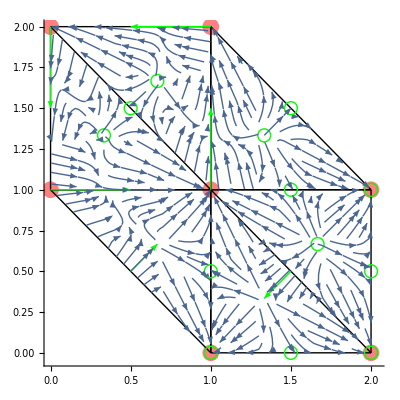

```mathematica
grida = getFullGrid[2,2];
grida[[1,1]]={0,1};
grida[[2,2]]={1,0};
v1a = {{{1,0},{0,1}},{{1,0},{0,1},{1,1}}};
v2a= {{{0,0},{1,0}},{{0,0},{1,0},{0,1}}};
v3a={{{1,1}},{{1,1},{1,2}}};
v4a={{{1,2}},{{1,2},{0,2}}};
v5a={{{0,2}},{{0,2},{0,1}}};
v6a={{{0,1}},{{0,1},{1,1}}};
v7a={{{1,1},{2,0}},{{1,1},{2,0},{1,0}}};
Va={v1a,v3a,v4a,v5a,v6a,v7a};
drawFullPlot[grida,Va]
```

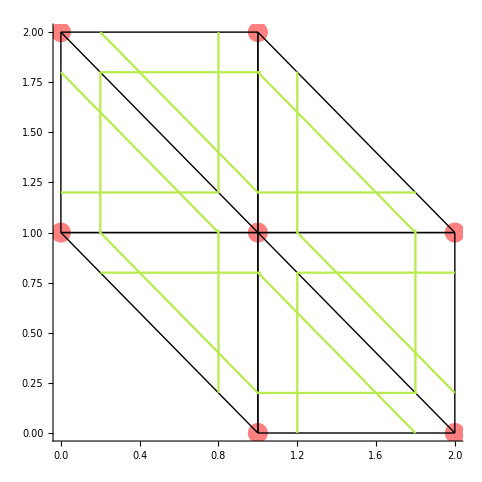

```mathematica
drawCellDecopositionWithComplex[grida,0.2]
```

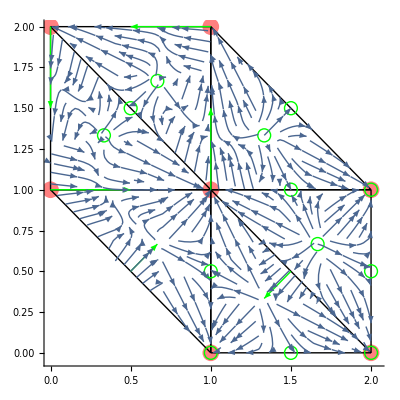

```mathematica
drawFullPlot[grida,Va]
```

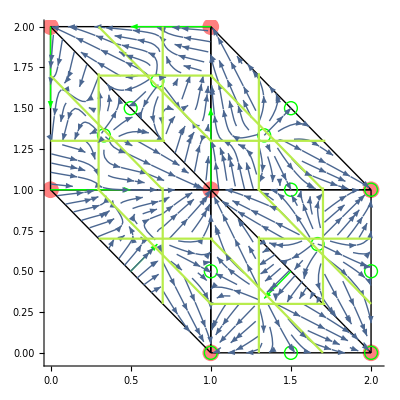

```mathematica
drawFullPlotWithCels[grida,Va,0.3]
```

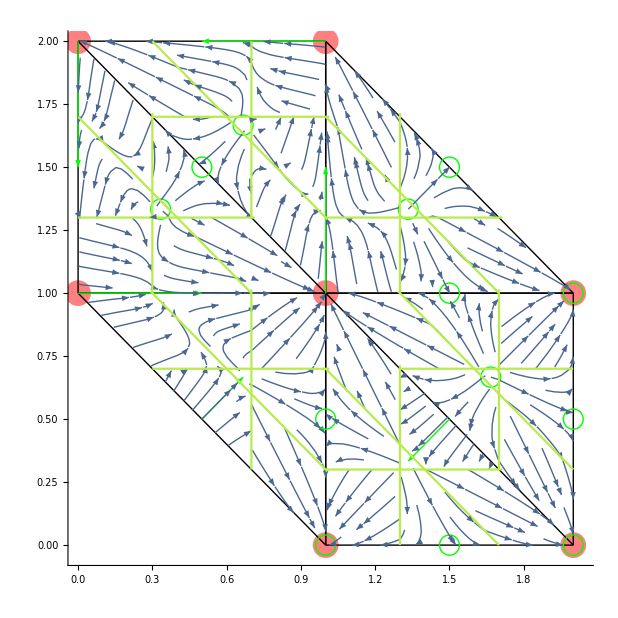
```mathematica
-Graphics-_□
```

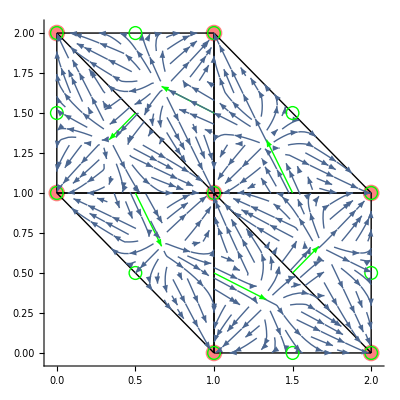

```mathematica
gridb = getFullGrid[2,2];
gridb[[1,1]]={0,1};
gridb[[2,2]]={1,0};
v1b = {{{1,0},{1,1}},{{1,0},{1,1},{2,0}}};
v2b={{{1,1},{2,0}},{{1,1},{2,0},{2,1}}};
v3b ={{{1,1},{2,1}},{{1,1},{2,1},{1,2}}};
v4b ={{{1,1},{1,2}},{{1,1},{1,2},{0,2}}};
v5b={{{1,1},{0,2}},{{1,1},{0,2},{0,1}}};
v6b ={{{1,1},{0,1}},{{1,1},{0,1},{1,0}}};
Vb = {v1b,v2b,v3b,v4b,v5b,v6b};
drawFullPlot[gridb,Vb]
```

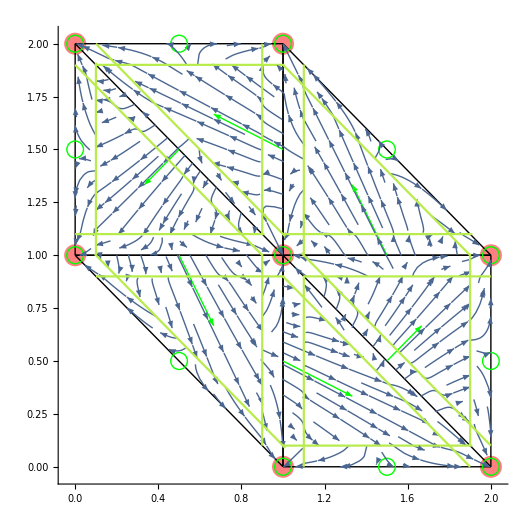

```mathematica
drawFullPlotWithCels[grida,Vb,0.1]
```

```mathematica
v7b={{{0,1}},{{0,1},{1,0}}};
v8b={{{1,0}},{{1,0},{2,0}}};
v9b={{{2,0}},{{2,0},{2,1}}};
v10b={{{2,1}},{{1,2},{2,1}}};
v11b={{{1,2}},{{1,2},{0,2}}};
v12b={{{0,2}},{{0,1},{0,2}}};
Vba = {v1b,v2b,v3b,v4b,v5b,v6b,v7b,v8b,v9b,v10b,v11b,v12b};
```

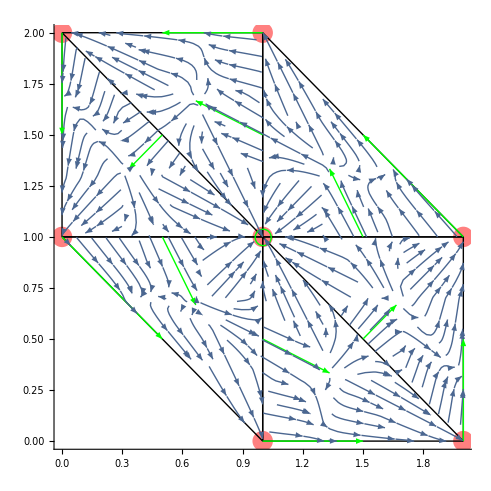

```mathematica
drawFullPlot[gridb,Vba]
```

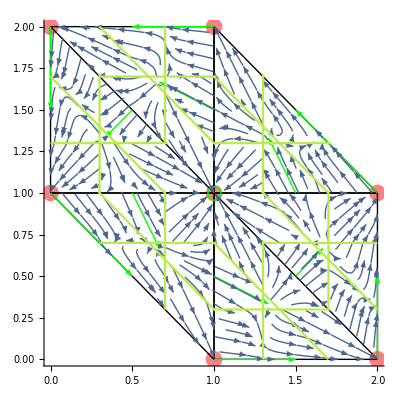

```mathematica
drawFullPlotWithCels[gridb,Vba,0.3]
```

```mathematica
gridd = getFullGrid[1,1];
gridd[[1,1]]={1,1};

v3d={{{0,0}},{{0,0},{1,0}}};
v4d={{{1,0}},{{1,0},{1,1}}};
v5d={{{1,1}},{{0,1},{1,1}}};
v6d={{{0,1}},{{0,1},{0,0}}};
v7d={{{0,1},{1,0}},{{0,1},{0,0},{1,0}}};
Vd={v3d,v4d,v5d,v6d,v7d};
```

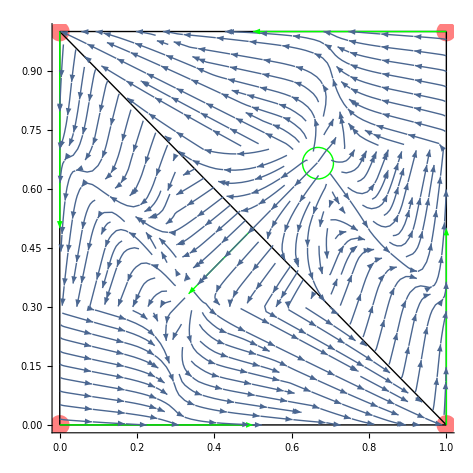

```mathematica
drawFullPlot[gridd,Vd]
```

```mathematica
gride = getFullGrid[3,3];
gride[[1,1]]={0,1};
gride[[3,3]]={1,0};
gride[[2,2]]={0,0};
```

```mathematica
ve1={{{1,1}},{{1,2},{1,1}}};
ve2={{{1,2}},{{1,2},{2,2}}};
ve3={{{2,2}},{{2,1},{2,2}}};
ve4={{{2,1}},{{2,1},{1,1}}};
ve5= {{{1,1},{1,0}},{{1,1},{1,0},{2,0}}};
ve6= {{{1,1},{2,0}},{{1,1},{2,1},{2,0}}};
ve7={{{2,1},{2,0}},{{3,0},{2,1},{2,0}}};
ve8={{{2,1},{3,0}},{{3,0},{2,1},{3,1}}};
ve9={{{2,1},{3,1}},{{2,2},{2,1},{3,1}}};
ve10={{{2,2},{3,1}},{{2,2},{3,2},{3,1}}};
ve11={{{2,2},{3,2}},{{2,2},{3,2},{2,3}}};
ve12={{{2,2},{2,3}},{{2,2},{1,3},{2,3}}};
ve13={{{2,2},{1,3}},{{2,2},{1,3},{1,2}}};
ve14={{{1,2},{1,3}},{{0,3},{1,3},{1,2}}};
ve15={{{1,2},{0,3}},{{0,3},{1,2},{0,2}}};
ve16={{{1,2},{0,2}},{{1,1},{1,2},{0,2}}};
ve17={{{1,1},{0,2}},{{1,1},{0,1},{0,2}}};
ve18={{{1,1},{0,1}},{{1,1},{0,1},{1,0}}};
ve19={{{1,0}},{{1,0},{0,1}}};
ve20={{{0,1}},{{0,2},{0,1}}};
ve21={{{0,2}},{{0,3},{0,2}}};
ve22={{{0,3}},{{0,3},{1,3}}};
ve23={{{1,3}},{{1,3},{2,3}}};
ve24 ={{{2,3}},{{2,3},{3,2}}};
ve25={{{3,2}},{{3,2},{3,1}}};
ve26={{{3,1}},{{3,0},{3,1}}};
ve27={{{3,0}},{{3,0},{2,0}}};
ve28={{{2,0}},{{2,0},{1,0}}};
Ve={ve1,ve2,ve3,ve4,ve5,ve6,ve7,ve8,ve9,ve10,ve11,ve12,ve13,ve14,ve15,ve16,ve17,ve18,ve19,ve20,ve21,ve22,ve23,ve24,ve25,ve26,ve27,ve28};
```

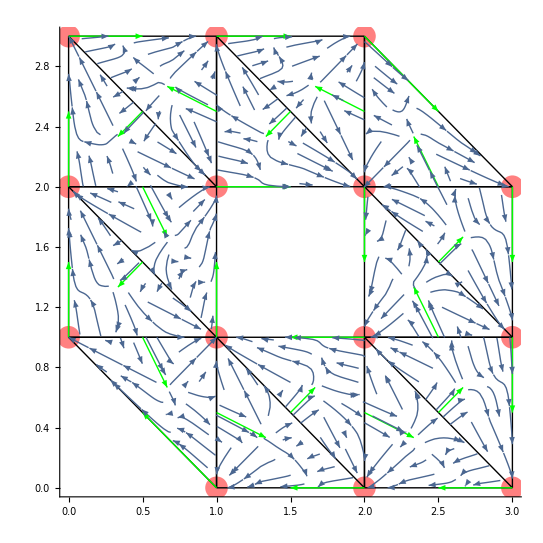

```mathematica
drawFullPlot[gride,Ve]
```